# Quantum Teleportation

by José Luis Gómez-Muñoz
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx

## Introduction

This is a tutorial on the use of Quantum`Computing` Mathematica add-on to simulate quantum teleportation.

## Load the Package

First load the Quantum`Computing` package. Write:
Needs["Quantum`Computing`"];
then press at the same time the keys ⇧-⌤ to evaluate. Mathematica will load the package:

```mathematica
Needs["Quantum`Computing`"]
```

Quantum`Computing` Version 2.2.0. (June 2010) 
A Mathematica package for Quantum Computing in Dirac bra-ket notation and plotting of quantum circuits
by José Luis Gómez-Muñoz

Execute SetComputingAliases[] in order to use the keyboard to enter quantum objects in Dirac's notation
SetComputingAliases[] must be executed again in each new notebook that is created

In order to use the keyboard to enter quantum objects write:
SetComputingAliases[ ];
then press at the same time the keys ⇧-⌤ to evaluate. The semicolon prevents Mathematica from printing the help message. Remember that SetComputingAliases[ ] must be evaluated again in each new notebook:

```mathematica
SetComputingAliases[];
```

## Quantum Teleportation

Below is the Quantum Teleportation circuit. Notice the syntaxis for specifying gates that are applied before the measurement and gates that are applied after the measurment.

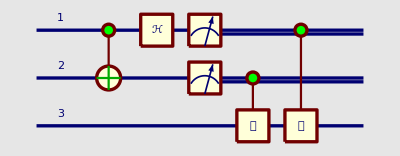

```mathematica
QuantumPlot[(𝒞^{OverHat[1]})[Subscript[𝒵, OverHat[3]]]·(𝒞^{OverHat[2]})[Subscript[𝒳, OverHat[3]]]·QubitMeasurement[Subscript[ℋ, OverHat[1]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]],{OverHat[1],OverHat[2]}]]
```

Actually, Quantum Teleportation requires the second and third qubits to be on their maximum entanglement state |ℬ_(00,OverHat[2],OverHat[3])⟩:

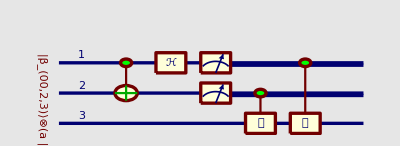

```mathematica
QuantumPlot[(𝒞^{OverHat[1]})[Subscript[𝒵, OverHat[3]]]·(𝒞^{OverHat[2]})[Subscript[𝒳, OverHat[3]]]·QubitMeasurement[Subscript[ℋ, OverHat[1]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·|Subscript[ℬ, 00,OverHat[2],OverHat[3]]⟩⊗(a|Subscript[0, OverHat[1]]⟩+b|Subscript[1, OverHat[1]]⟩),{OverHat[1],OverHat[2]}]]
```

QuantumEvaluate shows that this circuit actually "teleports" (cuts and pastes) a and b from the first qubit in the initial state:
(a|0_OverHat[1]⟩+b|1_OverHat[1]⟩)⊗|ℬ_(00,OverHat[2],OverHat[3])⟩ 
to the third qubit in the final state:
 |ψ_(OverHat[1],OverHat[2])⟩⊗(a|0_OverHat[3]⟩+b|1_OverHat[3]⟩) 
 (Below the final states include a normalization factor √(a a^*+b b^*))

```mathematica
QuantumEvaluate[(𝒞^{OverHat[1]})[Subscript[𝒵, OverHat[3]]]·(𝒞^{OverHat[2]})[Subscript[𝒳, OverHat[3]]]·QubitMeasurement[Subscript[ℋ, OverHat[1]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·|Subscript[ℬ, 00,OverHat[2],OverHat[3]]⟩⊗(a|Subscript[0, OverHat[1]]⟩+b|Subscript[1, OverHat[1]]⟩),{OverHat[1],OverHat[2]}]]
```

Probability | Measurement | State
1/4 | {{0_OverHat[1],0_OverHat[2]}} | |0_OverHat[1]⟩⊗|0_OverHat[2]⟩⊗((a |0_OverHat[3]⟩)/(√(a a^*+b b^*))+(b |1_OverHat[3]⟩)/(√(a a^*+b b^*)))
1/4 | {{0_OverHat[1],1_OverHat[2]}} | |0_OverHat[1]⟩⊗|1_OverHat[2]⟩⊗((a |0_OverHat[3]⟩)/(√(a a^*+b b^*))+(b |1_OverHat[3]⟩)/(√(a a^*+b b^*)))
1/4 | {{1_OverHat[1],0_OverHat[2]}} | |1_OverHat[1]⟩⊗|0_OverHat[2]⟩⊗((a |0_OverHat[3]⟩)/(√(a a^*+b b^*))+(b |1_OverHat[3]⟩)/(√(a a^*+b b^*)))
1/4 | {{1_OverHat[1],1_OverHat[2]}} | |1_OverHat[1]⟩⊗|1_OverHat[2]⟩⊗((a |0_OverHat[3]⟩)/(√(a a^*+b b^*))+(b |1_OverHat[3]⟩)/(√(a a^*+b b^*)))
Probability | Measurement | State

## Variation of Quantum Teleportation Circuit: Controlled Gates Commute with Measurements on the Control Qubits

Controlled gates commute with measurements on the control qubits. Therefore the Teleportation Circuit can have the measurements at the end:

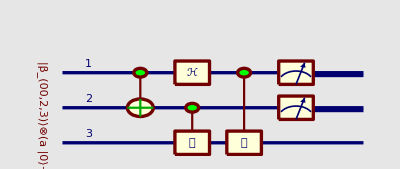

```mathematica
QuantumPlot[QubitMeasurement[(𝒞^{OverHat[1]})[Subscript[𝒵, OverHat[3]]]·(𝒞^{OverHat[2]})[Subscript[𝒳, OverHat[3]]]·Subscript[ℋ, OverHat[1]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·|Subscript[ℬ, 00,OverHat[2],OverHat[3]]⟩⊗(a|Subscript[0, OverHat[1]]⟩+b|Subscript[1, OverHat[1]]⟩),{OverHat[1],OverHat[2]}]]
```

Again Teleportation calculations, but this time with the measurement at the end. This circuit actually "teleports" (cuts and pastes) a and b from the first qubit in the initial state:
(a|0_OverHat[1]⟩+b|1_OverHat[1]⟩)⊗|ℬ_(00,OverHat[2],OverHat[3])⟩ 
to the third qubit in the final state:
 |ψ_(OverHat[1],OverHat[2])⟩⊗(a|0_OverHat[3]⟩+b|1_OverHat[3]⟩)
  (Below the final states include a normalization factor √(a a^*+b b^*))

```mathematica
QuantumEvaluate[QubitMeasurement[(𝒞^{OverHat[1]})[Subscript[𝒵, OverHat[3]]]·(𝒞^{OverHat[2]})[Subscript[𝒳, OverHat[3]]]·Subscript[ℋ, OverHat[1]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·|Subscript[ℬ, 00,OverHat[2],OverHat[3]]⟩⊗(a|Subscript[0, OverHat[1]]⟩+b|Subscript[1, OverHat[1]]⟩),{OverHat[1],OverHat[2]}]]
```

Probability | Measurement | State
1/4 | {{0_OverHat[1],0_OverHat[2]}} | |0_OverHat[1]⟩⊗|0_OverHat[2]⟩⊗((a |0_OverHat[3]⟩)/(√(a a^*+b b^*))+(b |1_OverHat[3]⟩)/(√(a a^*+b b^*)))
1/4 | {{0_OverHat[1],1_OverHat[2]}} | |0_OverHat[1]⟩⊗|1_OverHat[2]⟩⊗((a |0_OverHat[3]⟩)/(√(a a^*+b b^*))+(b |1_OverHat[3]⟩)/(√(a a^*+b b^*)))
1/4 | {{1_OverHat[1],0_OverHat[2]}} | |1_OverHat[1]⟩⊗|0_OverHat[2]⟩⊗((a |0_OverHat[3]⟩)/(√(a a^*+b b^*))+(b |1_OverHat[3]⟩)/(√(a a^*+b b^*)))
1/4 | {{1_OverHat[1],1_OverHat[2]}} | |1_OverHat[1]⟩⊗|1_OverHat[2]⟩⊗((a |0_OverHat[3]⟩)/(√(a a^*+b b^*))+(b |1_OverHat[3]⟩)/(√(a a^*+b b^*)))
Probability | Measurement | State

by José Luis Gómez-Muñoz
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx